```mathematica
M[T_]:=If[T< 2/Log[1+√2],(1-Sinh[2/T]^-4)^(1/8),0]
```

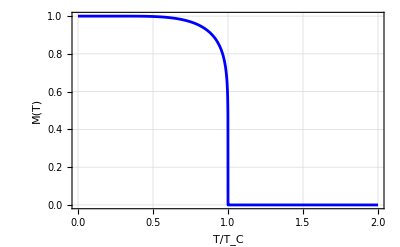

```mathematica
Plot[M[T*2/Log[1+√2]],{T,0,2},FrameLabel->{"T/T_C","M(T)"},LabelStyle->Directive[25], ImageSize->{800,800*(√5-1)/2},Frame->True,FrameTicksStyle->Directive[20],PlotStyle->{Thickness[0.005],Blue},GridLines->Automatic,GridLinesStyle->Dashed]
```